```mathematica
(*Make a list of initial conditions you want*)
```

```mathematica
mat2elem[AB_,Ab_,aB_,ab_,n_]:=(ab)*n*n*n+(aB)*n*n+(Ab)*n+AB+1
```

```mathematica
elem2mat[elem_,n_]:=elem2mat[elem,n]=Block[{out},
out=Table[0,{i,1,4}];
out[[1]]=Mod[elem-1,n];
out[[2]]=Mod[Floor[(elem-1)/n],n];
out[[3]]=Mod[Floor[(elem-1)/(n*n)],n];
out[[4]]=Mod[Floor[(elem-1)/(n*n*n)],n];
out
]
```

```mathematica
initlist=Flatten[Table[{{0,i,j,0},mat2elem[0,i,j,0,10]},{i,1,9},{j,0,9}],1];
```

```mathematica
absorblist1=Flatten[Table[{{i,9,j,k},mat2elem[i,9,j,k,10]},{i,0,9},{j,0,9},{k,0,9}],2];
absorblist2=Flatten[Table[{{9,i,j,k},mat2elem[9,i,j,k,10]},{i,0,8},{j,0,9},{k,0,9}],2];
absorblist=Join[{{{0,0,0,0},1}},absorblist1,absorblist2];
```

## Get absorbtionmatrices

```mathematica
datar050=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r050.mat"][[1]];
datar050Normal=Normal[datar050[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar050];
```

```mathematica
datar040=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r040.mat"][[1]];
datar040Normal=Normal[datar040[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar040]
```

```mathematica
datar030=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r030.mat"][[1]];
datar030Normal=Normal[datar030[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar030]
```

```mathematica
datar020=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r020.mat"][[1]];
datar020Normal=Normal[datar020[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar020]
```

```mathematica
datar010=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r010.mat"][[1]];
datar010Normal=Normal[datar010[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar010]
```

```mathematica
datar005=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r005.mat"][[1]];
datar005Normal=Normal[datar005[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar005]
```

```mathematica
datar000=Import["/home/freek/Documents/temp/Introgression/Matlab/data/Absorbptionmatrices/r000.mat"][[1]];
datar000Normal=Normal[datar000[[absorblist[[;;,2]],initlist[[;;,2]]]]]//Chop;
Clear[datar000]
```

```mathematica
data=datar050Normal[[1,;;]]
```

{0.836756,0.839932,0.841903,0.843252,0.844218,0.844924,0.845438,0.8458,0.846031,0.846145,0.689836,0.696578,0.701049,0.704209,0.706521,0.70824,0.709513,0.710425,0.711023,0.711323,0.557608,0.567533,0.574501,0.579611,0.583459,0.586391,0.588614,0.590246,0.591342,0.59191,0.438603,0.45089,0.459938,0.466817,0.472151,0.476324,0.479569,0.482014,0.483703,0.484603,0.331499,0.344982,0.355339,0.363483,0.369986,0.375211,0.379381,0.382609,0.384904,0.386167,0.235105,0.248301,0.258837,0.267398,0.274432,0.280238,0.284997,0.288785,0.291565,0.29315,0.14835,0.159444,0.168639,0.176353,0.182877,0.188408,0.193067,0.196888,0.199792,0.201523,0.0702712,0.0770941,0.0829634,0.0880491,0.0924769,0.0963356,0.0996769,0.102504,0.104743,0.106159,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[data]
```

90

```mathematica
datar000=datar050Normal[[1,;;]];
```

```mathematica
intlist=initlist[[;;,1]][[;;,{2,3}]];
```

```mathematica
datafix={1-datar000,intlist}//Transpose;
```

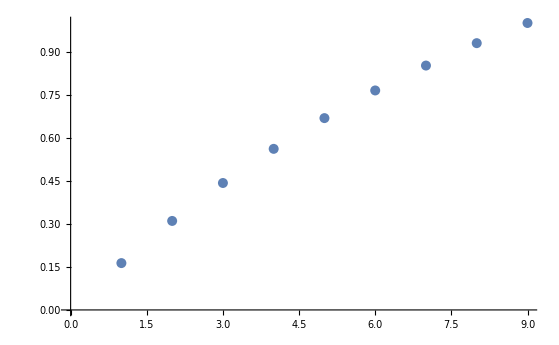

```mathematica
ListPlot[Table[datafix[[i]][[1]],{i,1,90,10}]]
```

```mathematica
datasim=Import["/home/freek/Documents/temp2/Introgression/Rfiles/data/fixationsimulations.csv"];
```

```mathematica
Fix[k_,s_]:=2 k s;
```

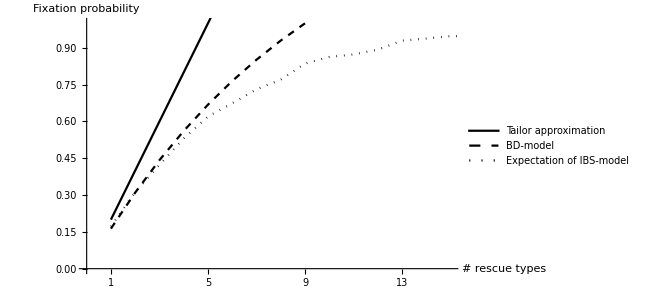

```mathematica
plot=Legended[Show[
{ListLinePlot[datasim,AxesLabel->{"# rescue types","Fixation probability"},Ticks->{Table[i,{i,1,20}], Automatic},PlotStyle->{Black,Dotted},PlotRange->{{0,15},{0,1}}],
ListLinePlot[Table[{i,Fix[i,.1]},{i,1,20}],PlotStyle->Black],
ListLinePlot[Table[datafix[[i]][[1]],{i,1,90,10}],PlotStyle->{Black,Dashed}]
}
],
Placed[
LineLegend[{
{Black},{Black,Dashed},{Black,Dotted},NULL
},
{
Style["Tailor approximation"],
Style["BD-model"],
Style["Expectation of IBS-model"]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{.7,0.2}
] 

]
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Rfiles/figures/FixationProb.eps",plot]
```

/home/freek/Documents/temp2/Introgression/Rfiles/figures/FixationProb.eps

```mathematica
outmats01=Import["/home/freek/Documents/temp2/Introgression/Matlab/outmats01.mat"][[5]];
outmats02=Import["/home/freek/Documents/temp2/Introgression/Matlab/outmats02.mat"][[5]];
outmats03=Import["/home/freek/Documents/temp2/Introgression/Matlab/outmats03.mat"][[5]];
```

```mathematica
ListLinePlot[outmats02]
```

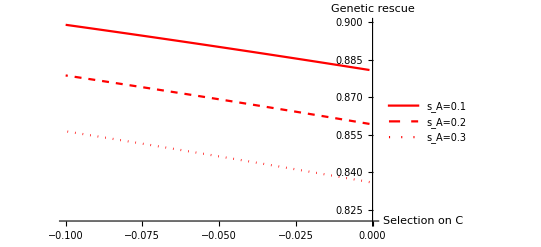

```mathematica
plot=Legended[Show[{
ListLinePlot[outmats01,PlotRange->{Automatic,{0.82,0.90}},PlotStyle->{Red},AxesLabel->{"Selection on C","Genetic rescue"}],
ListLinePlot[outmats02,PlotStyle->{Red,Dashed}],
ListLinePlot[outmats03, PlotStyle->{Red,Dotted}]
}
],LineLegend[{
{Red},{Red,Dashed},{Red,Dotted},NULL
},
{
"s_A=0.1",
"s_A=0.2",
"s_A=0.3"
}
]
]
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Matlab/Figures/3locuseffect.eps",plot]
```

/home/freek/Documents/temp2/Introgression/Matlab/Figures/3locuseffect.eps